```mathematica
nSpectrum=  (* Copy and paste from MCNP tally *)
"1.0000E-11 0.00000E+00 0.0000
1.2589E-11 0.00000E+00 0.0000
1.5849E-11 0.00000E+00 0.0000
1.9953E-11 0.00000E+00 0.0000
2.5119E-11 0.00000E+00 0.0000
3.1623E-11 0.00000E+00 0.0000
3.9811E-11 0.00000E+00 0.0000
5.0119E-11 0.00000E+00 0.0000
6.3096E-11 0.00000E+00 0.0000
7.9433E-11 0.00000E+00 0.0000
1.0000E-10 0.00000E+00 0.0000
1.2589E-10 0.00000E+00 0.0000
1.5849E-10 0.00000E+00 0.0000
1.9953E-10 0.00000E+00 0.0000
2.5119E-10 0.00000E+00 0.0000
3.1623E-10 0.00000E+00 0.0000
3.9811E-10 0.00000E+00 0.0000
5.0119E-10 0.00000E+00 0.0000
6.3096E-10 0.00000E+00 0.0000
7.9433E-10 0.00000E+00 0.0000
1.0000E-09 1.17462E-12 1.0000
1.2589E-09 2.69972E-12 0.5865
1.5849E-09 1.12794E-11 0.3668
1.9953E-09 6.17010E-12 0.3859
2.5119E-09 1.77844E-11 0.2815
3.1623E-09 1.99997E-11 0.2814
3.9811E-09 2.29298E-11 0.2396
5.0119E-09 5.06395E-11 0.1629
6.3096E-09 5.01774E-11 0.1761
7.9433E-09 1.21768E-10 0.1133
1.0000E-08 1.93071E-10 0.0896
1.2589E-08 3.00676E-10 0.0695
1.5849E-08 3.92578E-10 0.0620
1.9953E-08 5.58730E-10 0.0583
2.5119E-08 6.65225E-10 0.0475
3.1623E-08 1.02952E-09 0.0422
3.9811E-08 1.17170E-09 0.0365
5.0119E-08 1.36881E-09 0.0331
6.3096E-08 1.48441E-09 0.0354
7.9433E-08 1.31475E-09 0.0347
1.0000E-07 1.07873E-09 0.0404
1.2589E-07 7.77606E-10 0.0511
1.5849E-07 4.59251E-10 0.0616
1.9953E-07 2.25601E-10 0.0947
2.5119E-07 1.03784E-10 0.1371
3.1623E-07 4.99252E-11 0.2280
3.9811E-07 6.33702E-11 0.2284
5.0119E-07 5.64905E-11 0.2187
6.3096E-07 4.69694E-11 0.2756
7.9433E-07 4.14403E-11 0.2501
1.0000E-06 4.21168E-11 0.2501
1.2589E-06 5.39134E-11 0.2355
1.5849E-06 3.87049E-11 0.2693
1.9953E-06 5.54643E-11 0.2515
2.5119E-06 4.45629E-11 0.2538
3.1623E-06 3.93953E-11 0.2583
3.9811E-06 4.02175E-11 0.2585
5.0119E-06 8.94484E-11 0.4730
6.3096E-06 3.90342E-11 0.2583
7.9433E-06 3.97939E-11 0.2584
1.0000E-05 2.41093E-11 0.3337
1.2589E-05 4.48070E-11 0.2802
1.5849E-05 2.55097E-11 0.3375
1.9953E-05 5.25053E-11 0.2679
2.5119E-05 8.66888E-11 0.1895
3.1623E-05 5.26199E-11 0.2307
3.9811E-05 5.58519E-11 0.2556
5.0119E-05 4.96734E-11 0.3221
6.3096E-05 4.80254E-11 0.2359
7.9433E-05 4.34604E-11 0.2512
1.0000E-04 2.42176E-11 0.3339
1.2589E-04 3.47153E-11 0.2799
1.5849E-04 1.89696E-11 0.3790
1.9953E-04 3.17222E-11 0.2863
2.5119E-04 2.48090E-11 0.3214
3.1623E-04 4.93945E-11 0.2495
3.9811E-04 4.39920E-11 0.2517
5.0119E-04 3.95966E-11 0.2700
6.3096E-04 5.05098E-11 0.2426
7.9433E-04 4.48834E-11 0.2428
1.0000E-03 4.23622E-11 0.2502
1.2589E-03 3.72796E-11 0.2676
1.5849E-03 4.30344E-11 0.2612
1.9953E-03 6.21278E-11 0.2108
2.5119E-03 6.02238E-11 0.2086
3.1623E-03 5.55197E-11 0.2184
3.9811E-03 4.96195E-11 0.3393
5.0119E-03 3.05136E-11 0.3035
6.3096E-03 6.17183E-11 0.2145
7.9433E-03 6.23169E-11 0.3316
1.0000E-02 1.90917E-11 0.4271
1.2589E-02 8.15067E-11 0.1806
1.5849E-02 2.92109E-11 0.3018
1.9953E-02 3.65349E-11 0.2674
2.5119E-02 4.80619E-11 0.2506
3.1623E-02 3.77052E-11 0.2676
3.9811E-02 5.59729E-11 0.2184
5.0119E-02 6.20424E-11 0.2073
6.3096E-02 5.59628E-11 0.2187
7.9433E-02 7.16933E-11 0.1926
1.0000E-01 7.54519E-11 0.1892
1.2589E-01 8.01383E-11 0.1828
1.5849E-01 8.62300E-11 0.1771
1.9953E-01 1.34709E-10 0.1588
2.5119E-01 1.10956E-10 0.1891
3.1623E-01 1.62720E-10 0.1355
3.9811E-01 1.84578E-10 0.1220
5.0119E-01 1.89533E-10 0.1185
6.3096E-01 2.56288E-10 0.1016
7.9433E-01 3.31870E-10 0.0902
1.0000E+00 4.04089E-10 0.0812
1.2589E+00 5.04953E-10 0.0730
1.5849E+00 7.55299E-10 0.0619
1.9953E+00 8.97612E-10 0.0541
2.5119E+00 1.99332E-09 0.0362
3.1623E+00 0.00000E+00 0.0000
3.9811E+00 0.00000E+00 0.0000
5.0119E+00 0.00000E+00 0.0000
6.3096E+00 0.00000E+00 0.0000
7.9433E+00 0.00000E+00 0.0000
1.0000E+01 0.00000E+00 0.0000";
```

```mathematica
{eList,nList,errList} = Transpose[ImportString[nSpectrum,"Table"]];
```

```mathematica
toPlot = Transpose[{Drop[eList,-1],Drop[nList,1]}];
```

```mathematica
myTicks={10^#,Superscript[10,#]}&/@Range[-9,1];
```

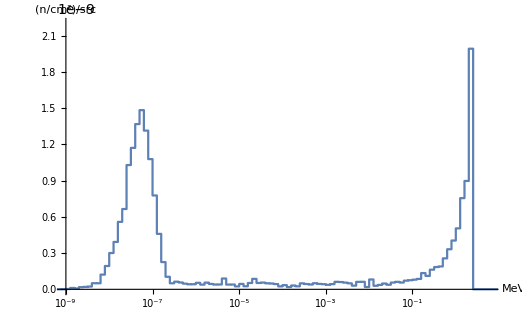

```mathematica
nPlot=ListStepPlot[toPlot,ScalingFunctions->{"Log10"},PlotRange->{{10^-9,6},{0,2.2 10^-9}},
AxesLabel->{"MeV","(n/cm^2)/src"},
Ticks->{myTicks,Automatic}]
```

```mathematica
pSpectrum="1.0000E-11 0.00000E+00 0.0000
1.2589E-11 0.00000E+00 0.0000
1.5849E-11 0.00000E+00 0.0000
1.9953E-11 0.00000E+00 0.0000
2.5119E-11 0.00000E+00 0.0000
3.1623E-11 0.00000E+00 0.0000
3.9811E-11 0.00000E+00 0.0000
5.0119E-11 0.00000E+00 0.0000
6.3096E-11 0.00000E+00 0.0000
7.9433E-11 0.00000E+00 0.0000
1.0000E-10 0.00000E+00 0.0000
1.2589E-10 0.00000E+00 0.0000
1.5849E-10 0.00000E+00 0.0000
1.9953E-10 0.00000E+00 0.0000
2.5119E-10 0.00000E+00 0.0000
3.1623E-10 0.00000E+00 0.0000
3.9811E-10 0.00000E+00 0.0000
5.0119E-10 0.00000E+00 0.0000
6.3096E-10 0.00000E+00 0.0000
7.9433E-10 0.00000E+00 0.0000
1.0000E-09 0.00000E+00 0.0000
1.2589E-09 0.00000E+00 0.0000
1.5849E-09 0.00000E+00 0.0000
1.9953E-09 0.00000E+00 0.0000
2.5119E-09 0.00000E+00 0.0000
3.1623E-09 0.00000E+00 0.0000
3.9811E-09 0.00000E+00 0.0000
5.0119E-09 0.00000E+00 0.0000
6.3096E-09 0.00000E+00 0.0000
7.9433E-09 0.00000E+00 0.0000
1.0000E-08 0.00000E+00 0.0000
1.2589E-08 0.00000E+00 0.0000
1.5849E-08 0.00000E+00 0.0000
1.9953E-08 0.00000E+00 0.0000
2.5119E-08 0.00000E+00 0.0000
3.1623E-08 0.00000E+00 0.0000
3.9811E-08 0.00000E+00 0.0000
5.0119E-08 0.00000E+00 0.0000
6.3096E-08 0.00000E+00 0.0000
7.9433E-08 0.00000E+00 0.0000
1.0000E-07 0.00000E+00 0.0000
1.2589E-07 0.00000E+00 0.0000
1.5849E-07 0.00000E+00 0.0000
1.9953E-07 0.00000E+00 0.0000
2.5119E-07 0.00000E+00 0.0000
3.1623E-07 0.00000E+00 0.0000
3.9811E-07 0.00000E+00 0.0000
5.0119E-07 0.00000E+00 0.0000
6.3096E-07 0.00000E+00 0.0000
7.9433E-07 0.00000E+00 0.0000
1.0000E-06 0.00000E+00 0.0000
1.2589E-06 0.00000E+00 0.0000
1.5849E-06 0.00000E+00 0.0000
1.9953E-06 0.00000E+00 0.0000
2.5119E-06 0.00000E+00 0.0000
3.1623E-06 0.00000E+00 0.0000
3.9811E-06 0.00000E+00 0.0000
5.0119E-06 0.00000E+00 0.0000
6.3096E-06 0.00000E+00 0.0000
7.9433E-06 0.00000E+00 0.0000
1.0000E-05 0.00000E+00 0.0000
1.2589E-05 0.00000E+00 0.0000
1.5849E-05 0.00000E+00 0.0000
1.9953E-05 0.00000E+00 0.0000
2.5119E-05 0.00000E+00 0.0000
3.1623E-05 0.00000E+00 0.0000
3.9811E-05 0.00000E+00 0.0000
5.0119E-05 0.00000E+00 0.0000
6.3096E-05 0.00000E+00 0.0000
7.9433E-05 0.00000E+00 0.0000
1.0000E-04 0.00000E+00 0.0000
1.2589E-04 0.00000E+00 0.0000
1.5849E-04 0.00000E+00 0.0000
1.9953E-04 0.00000E+00 0.0000
2.5119E-04 0.00000E+00 0.0000
3.1623E-04 0.00000E+00 0.0000
3.9811E-04 0.00000E+00 0.0000
5.0119E-04 0.00000E+00 0.0000
6.3096E-04 0.00000E+00 0.0000
7.9433E-04 0.00000E+00 0.0000
1.0000E-03 0.00000E+00 0.0000
1.2589E-03 0.00000E+00 0.0000
1.5849E-03 0.00000E+00 0.0000
1.9953E-03 0.00000E+00 0.0000
2.5119E-03 0.00000E+00 0.0000
3.1623E-03 0.00000E+00 0.0000
3.9811E-03 2.97788E-12 1.0000
5.0119E-03 0.00000E+00 0.0000
6.3096E-03 5.56326E-12 0.7080
7.9433E-03 5.19126E-12 0.7072
1.0000E-02 8.05828E-12 0.5782
1.2589E-02 2.18009E-11 0.3547
1.5849E-02 5.00406E-11 0.2376
1.9953E-02 1.73497E-10 0.1325
2.5119E-02 1.84286E-09 0.0450
3.1623E-02 8.96403E-09 0.0194
3.9811E-02 1.91451E-08 0.0149
5.0119E-02 2.62443E-08 0.0113
6.3096E-02 2.90867E-08 0.0116
7.9433E-02 3.00026E-08 0.0140
1.0000E-01 2.81533E-08 0.0104
1.2589E-01 2.73848E-08 0.0103
1.5849E-01 2.60005E-08 0.0106
1.9953E-01 2.28350E-08 0.0115
2.5119E-01 2.29846E-08 0.0117
3.1623E-01 2.21510E-08 0.0116
3.9811E-01 2.28858E-08 0.0111
5.0119E-01 2.30360E-08 0.0110
6.3096E-01 2.50332E-08 0.0104
7.9433E-01 2.41722E-08 0.0105
1.0000E+00 2.51660E-08 0.0103
1.2589E+00 2.73456E-08 0.0098
1.5849E+00 2.98154E-08 0.0094
1.9953E+00 3.52337E-08 0.0086
2.5119E+00 1.98572E-07 0.0037
3.1623E+00 1.63192E-10 0.1270
3.9811E+00 5.72422E-10 0.0702
5.0119E+00 1.28738E-09 0.0452
6.3096E+00 2.90175E-11 0.3391
7.9433E+00 1.83993E-11 0.3781
1.0000E+01 5.33631E-12 0.7072
1.2589E+01 5.36207E-12 0.7071
1.5849E+01 0.00000E+00 0.0000
1.9953E+01 0.00000E+00 0.0000
2.5119E+01 0.00000E+00 0.0000
3.1623E+01 0.00000E+00 0.0000
3.9811E+01 0.00000E+00 0.0000
5.0119E+01 0.00000E+00 0.0000
6.3096E+01 0.00000E+00 0.0000
7.9433E+01 0.00000E+00 0.0000
1.0000E+02 0.00000E+00 0.0000";
```

```mathematica
{peList,pnList,perrList} = Transpose[ImportString[pSpectrum,"Table"]];
```

```mathematica
ptoPlot = Transpose[{Drop[peList,-1],Drop[pnList,1]}];
```

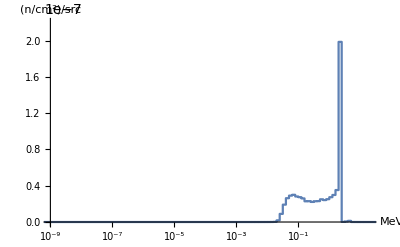

```mathematica
pPlot=ListStepPlot[ptoPlot,ScalingFunctions->{"Log10"},PlotRange->{{10^-9,20},{0,2.2 10^-7}},
AxesLabel->{"MeV","(n/cm^2)/src"},
Ticks->{myTicks,Automatic}]
```

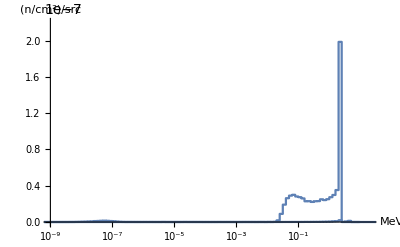

```mathematica
Show[pPlot,nPlot]
```

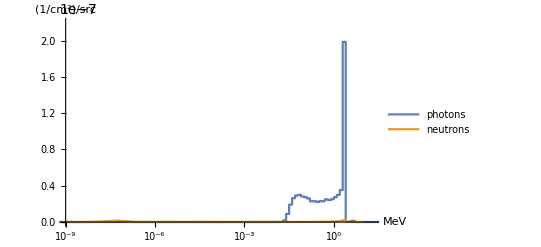

```mathematica
pPlot=ListStepPlot[{ptoPlot,toPlot},ScalingFunctions->{"Log10"},PlotRange->{{10^-9,20},{0,2.2 10^-7}},
AxesLabel->{"MeV","(1/cm^2)/src"},
Ticks->{myTicks,Automatic},PlotLegends->{"photons","neutrons"}]
```

```mathematica
(4π(300^2))^-1 // N
```

8.84194×10^-7